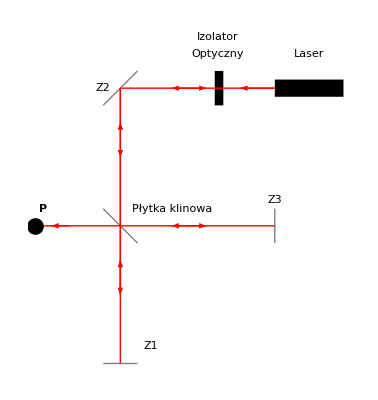

```mathematica
Show[


Graphics[{Gray,Thick,  Line[{{5,0},{6,0}}], Black,   Text[Style["Z1",Medium, Black], {6.4,0.5}]   }] ,
Graphics[{Gray,Thick,  Line[{{10,3.5},{10,4.5}}], Black,   Text[Style["Z3",Medium, Black], {10,4.75}]   }] ,
Graphics[{Gray,Thick,  Line[{{5,7.5},{6,8.5}}], Black,  Text[Style["Z2",Medium, Black], {5,8}]   }] ,
Graphics[{Gray,Thick,  Line[{{5,4.5},{6,3.5}}], Black,   Text[Style["Płytka klinowa",Medium, Black], {7,4.5}]   }] ,

Graphics[{Black,Rectangle[{8.25,7.5},{8.5,8.5}],     Text[Style["Izolator",Medium, Black], {8.33,9.5}],   Text[Style["Optyczny",Medium, Black], {8.33,9}]  }],
Graphics[{Black,Rectangle[{10,7.75},{12,8.25}],   Text[Style["Laser",Medium, Black], {11,9}]  }],

Graphics[{Red, Arrowheads[.03],Arrow[ {{5.5, 0},{5.5,3}}],  Arrow[{ {5.5,2},{5.5,7}}] ,   Arrow[{ {5.5,7},{5.5,8}, {8,8}}], 
 Arrow[{ {10,8},{9,8}}] }],
Graphics[{Red, Arrowheads[.03],Arrow[ {{5.5, 6},{5.5,2}}],  Arrow[{ {5.5,8},{5.5,6}}] ,   Arrow[{ {10,8}, {7,8}}]     }],
Graphics[{Red, Arrowheads[.03],Arrow[ {{3, 4},{8,4}}],  Arrow[{ {10,4},{7,4}}] ,   Arrow[{ {4,4}, {3.5,4}}]     }],
Graphics[ {Black,PointSize[0.03], Point[{3,4}],  Text[Style["P",Bold,Medium, Black], {3.25,4.5}]}]

]
```

```mathematica
Show[
Graphics[{ Red, Arrowheads[0.03], Arrow[{{0,0 }, {4,0}}], Arrow[{{3.9,0}, {6,0}, {10,0}}],  Line[{{10,0}, {15.75,0}, {11,-3}}] }],
Graphics[{ Red, Arrowheads[0.03], Line[{{5,0 }, {-4.3,-7.75}}]    }],

Graphics[{ Red,Opacity[0.25], Triangle[{ {-4,-7.5}, {-6.5, -9.25}, {-6.5,-9.75} }]  }],
Graphics[{ Red,Opacity[0.25], Triangle[{ {-10,-9.5}, {7.2, -11}, {8.8,-10} }]  }],
Graphics[{ Red,Opacity[0.25], Triangle[{ {11,-3}, {4,-6.6}, {5,-7.3} }]  }],

Graphics[{Black,Rectangle[{-3,-0.5},{0,0.5}/2],    Text[Style["Laser",Black,Medium], {-1.5,1}]  }],
Graphics[{Gray, Thick, Line[{ {9.5, 0.5}/2, {10.5,-0.5}/2 }] ,    Text[Style["Płytka",Medium, Black], {5,1}]   }],
Graphics[{Gray, Rectangle[{ -13.5, -18}/2, {-13,-20}/2], Text[Style["Z2",Black,Medium], {-6.5,-8}], White, Rectangle[{-11,-9},{-6.75,-10}]   }],
Graphics[{Gray, Thick, Rectangle[ {31.5, 1}/2, {32,-1}/2 ] ,    Text[Style["Z1",Black,Medium], {15,1}]   }],
Graphics[{Black, PointSize[0.045], Point[{4.5, -7}] , Text[Style["P",Large,Bold,Medium], {3.5,-6} ]}],
Graphics[{Gray, Thick, Line[{ {-7+14, -11}, {-5+14,-10} }] ,   Text[Style["Klisza",Black,Medium], {11,-10}]   }],
Graphics[{Gray,Rotate[Rectangle[{-3.9,-7.5},{-4.9,-8}],-50Degree],     Text[Style["S2",Black,Medium], {-3,-8}] }],
Graphics[{Gray,Rotate[Rectangle[{10.4,-2.6},{11,-3.7}],35Degree],     Text[Style["S1",Black,Medium], {12,-3}] }],


Graphics[{ Red,Opacity[0.1], Triangle[{ {4.2,-6.6}, {7,-11}, {8.8,-10} }]  }],
Graphics[{ Red,Opacity[0.15], Triangle[{ {5,-7.3}, {7,-11}, {8.8,-10} }]  }],
PlotRange-> { {-7,16},{-12,2} }
]
```

-Graphics-

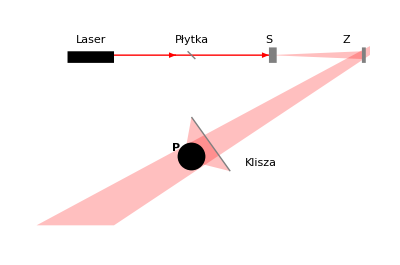

```mathematica
Show[
Graphics[{ Red, Arrowheads[0.03], Arrow[{{0,0 }, {4,0}}], Arrow[{{3.9,0}, {6,0}, {10,0}}] }],

Graphics[{ Red,Opacity[0.25], Triangle[{ {10,0}, {16,-0.25}, {16, 0.25} }]  }],
Graphics[{ Red,Opacity[0.25], Triangle[{ {4.5,-6.75}, {7.5,-7.5}, {5, -4} }]  }],
Graphics[{ Red,Opacity[0.25], Triangle[{ {21,3}, {-5,-11}, {0, -11} }]  }],

Graphics[{Black,Rectangle[{-3,-0.5},{0,0.5}/2],    Text[Style["Laser",Black,Medium], {-1.5,1}]  }],
Graphics[{Gray, Thick, Line[{ {9.5, 0.5}/2, {10.5,-0.5}/2 }] ,    Text[Style["Płytka",Medium, Black], {5,1}]   }],
Graphics[{Gray, Thick, Rectangle[ {32.5, 1}/2, {32,-1}/2 ] ,    Text[Style["Z",Black,Medium], {15,1}]   }],
Graphics[{Gray, Rectangle[{10,-0.5}, {10.5, 0.5}],    Text[Style["S",Black,Medium], {10,1}]}],
Graphics[{Black, PointSize[0.05], Point[{5,-6.5}],   Text[Style["P",Bold, Black,Medium], {4,-6}]}],
Graphics[{Gray,Thick, Line[{ {5,-4} , {7.5,-7.5}}],  Text[Style["Klisza", Black,Medium], {9.5,-7}]  }],
PlotRange->{{-5,16.1}, {-12,2} }
]
```